```mathematica
url="http://pages.mtu.edu/~dnaneet/thermo/hptr_dense_1.txt";
datasetDirty=Import[url, "Data"];
(*names={'celcius','bar','region','kJPerKg'}*)
s=Dimensions[datasetDirty][[1]];
dataset=Select[datasetDirty, #[[3]]≠ 0&]; (*Select only those rows and columns with non zero region*)
s=Dimensions[dataset][[1]];
```

```mathematica
T=dataset[[2;;s,1]]; (*temperature, C*)
P=dataset[[2;;s,2]]; (*pressure, bar*)
r=dataset[[2;;s,3]]/.{0->"r0",1->"r1", 2->"r2", 3->"r3", 4->"r4", 5->"r5"}; (*region, class/label*)
h=dataset[[2;;s,4]]; (*specific enthalpy, kJ/kg*)
```

```mathematica
thermoState=Thread[{T,P}]; (*thermodynamic state*)
mldata=RandomSample[Thread[thermoState->h]];
```

```mathematica
mldata
```

{{350,341}→1599.36,{110,536}→500.765,{685,456}→3594.85,{500,946}→2333.39,{370,746}→1658.96,{1210,81}→5161.42,{210,341}→910.71,{95,701}→451.788,36563,{450,806}→2085.85,{180,626}→797.716,{1345,26}→5529.61,{770,96}→4043.2,{675,166}→3765.35,{1080,26}→4836.59,{750,541}→3752.02,{580,721}→2946.37}
 |  |  |  |

```mathematica
f=NetChain[{LinearLayer[12],64,Tanh,32,Tanh,8,1},"Input"->2]
f=NetInitialize[f];
```

NetChain[<>]

```mathematica
s=Dimensions[mldata][[1]];
mldata2=Table[mldata[[i,1]]->{mldata[[i,2]]},{i,1,s-1,1}];
training=mldata2[[1;;s-1,All]];
```

```mathematica
trainedData=NetTrain[f,training]
```

NetChain[<>]

```mathematica
hStan[T0_, P0_]:=Module[{T=T0,P=P0},
ThermodynamicData["Water","Enthalpy",{"Temperature"->Quantity[T,"DegreesCelcius"],"Pressure"->Quantity[P,"Bar"]}][[1]]
];
```

```mathematica
p=1;
Table[((hStan(i,p))/1000- trainedData[{i,p}])*100/ trainedData[{i,1}],{i,1,1000,25}]//Flatten
```

{-101.748,321.069,70.2324,70.0103,204.366,24.8118,18.692,18.4738,16.5788,12.2019,8.0432,6.94066,5.15815,3.61603,2.03372,0.305461,-1.28195,-2.37018,-2.78621,-2.58373,-1.93311,-1.02087,-0.0158185,0.919913,1.60591,1.83435,1.4178,0.329303,-1.14998,-2.5079,-3.32566,-3.48533,-3.094,-2.32419,-1.32582,-0.208128,0.949173,2.07889,3.10994,3.95351}

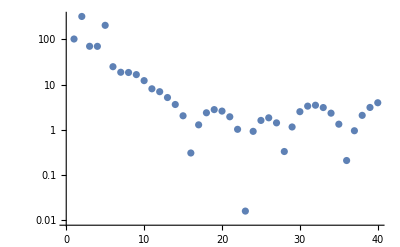

```mathematica
ListLogPlot[Abs[%]]
```